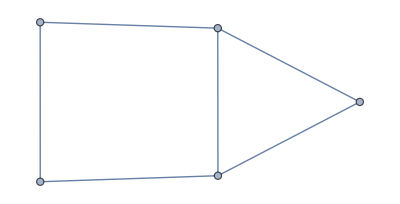

```mathematica
G=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->3}]
```

```mathematica
M=AdjacencyMatrix[G]
```

SparseArray[…]

```mathematica
H=AdjacencyGraph[M]
```

-Graphics-

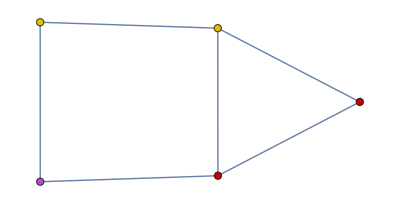

```mathematica
HighlightGraph[H,{{1,2},{3,4},{5}}]
```